```mathematica
u0=1.*10^-8;α=0.01;V[r_]=-α/r;δa[r_]:=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);
Veff[c_][r_]:=-α/r Erf[r/(√2 a)]-2π α c a^2 δa[r];
m=100.;l=0;l1=-1/2+√((l+1/2)^2-(α)^2);
kr:=√((e+m)^2-m^2);knr:=√(2 m e);γ:=(*(√(k^2+m^2) α)/k*)(α m)/k;
er:=√(m^2+k^2);enr:=k^2/(2m);
r2=u0;
r1=50.;
re=1000.;
```

```mathematica
Block[{a=0.01},Veff[c][r]]
```

-0.398942 c ⅇ^(-5000. r^2)-(0.01 Erf[70.7107 r])/r

```mathematica
WList={10^-10,10^-8,10^-5,.001,.003,.007,.01,.03,.07,.1,.3,.7,1};
```

```mathematica
Realδ=Module[{EE,(*k,*)Z=1,R,CC,u,f,r0,rule,W,γγ},
Table[
(* Define R(r) *)
W=√(k^2+m^2);
EE=W+m;
(*k=√(EE^2-m^2);*)γγ[k_]:=(√(k^2+m^2) Z α)/k;
R[r_]=r^l1 ⅇ^(-ⅈ k r)Hypergeometric1F1[Chop[l1+1+ⅈ γγ[k]],2l1+2,2ⅈ k r];
CC=(Gamma[2l1+2] ⅇ^(-(π/2)γ))/(Abs@Gamma[l1+1+ⅈ γγ[k]](2k)^(l1+1));
R[r_]=1/CC R[r];
(* Find Subscript[δ, l] *)
u[r_]=r R[r];
f[r_]=Simplify[D[u[r], r]/u[r]];
r0=50;(* Choose Subscript[r, 0] *)
rule=Chop@FindRoot[f[r0]==(k+γγ[k]/r0)Cot[k r0+δ(*+Log[2 k r0]/k*)](*Cot[k r0 -(l1 π)/2+γ Log[2k r0]+δ]*),{δ,0}];
Mod[δ/.rule,π,-π/2]
,{k,WList}]];
```

```mathematica
alist=Table[10^s,{s,-2,0,0.01}];
```

```mathematica
k=10^-10;
sol1=ParametricNDSolve[{-f''[x]+2m Veff[c][x]f[x]-(enr-Veff[c][x])^2/4 f[x]==2m enr f[x],f'[r2]==1,f[r2]==u0},f,{x,r1,r2},c,AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50]
```

{f→ParametricFunction[<>]}

```mathematica
Block[{c,a=0.25,sol1},{sol1=ParametricNDSolve[{-f''[x]+2m Veff[c][x]f[x]-(enr-Veff[c][x])^2/4 f[x]==2m enr f[x],f'[r2]==1,f[r2]==u0},f,{x,r1,r2},c,AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50];c=c/.FindRoot[(f[c]'[r1] ((enr-Veff[c][r1])/(8 m)+1)-(f[c][r1] Veff[c]'[r1])/(8 m))/((1+(enr-Veff[c][r1])/(8 m)) f[c][r1])==(k+γ/r1) Cot[k r1+Realδ[[1]]](*Cot[k r1-(l1 π)/2+γ Log[2k r1]+Realva[[1]]]*)/.sol1,{c,3,2},WorkingPrecision->30,MaxIterations->100,PrecisionGoal->6],(f[c]'[r1] ((enr-Veff[c][r1])/(8 m)+1)-(f[c][r1] Veff[c]'[r1])/(8 m))/((1+(enr-Veff[c][r1])/(8 m)) f[c][r1])-(k+γ/r1) Cot[k r1+Realδ[[1]]](*Cot[k r1-(l1 π)/2+γ Log[2k r1]+Realva[[1]]]*)/.sol1}]
```

FindRoot::precw: 参数函数的精度 (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«3»,{NDSolve`base$145650,«33»[«10»]}][c]'[50.]«1»0.00125 «1»«1»ParametricFunction[1,«4»,{NDSolve`base$145650,«33»[0,{«4»},«6»,{},All]}][c][50.])/((1+0.00125 (0.0002+2.05746280202619×10^-8688 c)) ParametricFunction[1,«4»,{NDSolve`base$145650,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) 小于 WorkingPrecision (30.).

ParametricNDSolve::precw: 微分方程的精度 ({{200. (-0.0159577 c$145643 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$145644]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$145644]-f''[x$145644]==1.×10^-20 f[x$145644],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

{1.28667263936162775261779231445,-1.11022×10^-16}

```mathematica
ParallelTable[Block[{c,sol1},sol1=ParametricNDSolve[{-f''[x]+2m Veff[c][x]f[x]-(enr-Veff[c][x])^2/4 f[x]==2m enr f[x],f'[r2]==1,f[r2]==u0},f,{x,r1,r2},c,AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50];{c=c/.FindRoot[(f[c]'[r1] ((enr-Veff[c][r1])/(8 m)+1)-(f[c][r1] Veff[c]'[r1])/(8 m))/((1+(enr-Veff[c][r1])/(8m))f[c][r1])==(k+γ/r1) Cot[k r1+Realδ[[1]]](*Cot[k r1 -(l1 π)/2+γ Log[2k r1]+Realva[[1]]]*)/.sol1,{c,3,2},WorkingPrecision->30,MaxIterations->100,PrecisionGoal->6],
(f[c]'[r1] ((enr-Veff[c][r1])/(8 m)+1)-(f[c][r1] Veff[c]'[r1])/(8 m))/((1+(enr-Veff[c][r1])/(8 m)) f[c][r1])-(k+γ/r1) Cot[k r1+Realδ[[1]]](*Cot[k r1-(l1 π)/2+γ Log[2k r1]+Realva[[1]]]*)/.sol1}],{a,alist}]
```

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,«4»,{NDSolve`base$6756,«33»[«10»]}][c]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$6756,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+3.77676026244693×10^-5428682 c)) «1»)==0.499393) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$12488,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$12488,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+1.90741300680385×10^-1363624 c)) ParametricFunction[1,«4»,{NDSolve`base$12488,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,«4»,{NDSolve`base$9154,«33»[«10»]}][c]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$9154,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+2.42454343980712×10^-342528 c)) ParametricFunction[1,«4»,{NDSolve`base$9154,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,«4»,{NDSolve`base$9109,«33»[«10»]}][c]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$9109,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+8.03384742461677×10^-86041 c)) «1»)==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.398942 c$6749 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$6750]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$6750]-f''[x$6750]==1.×10^-20 f[x$6750],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.199945 c$12481 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$12482]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$12482]-f''[x$12482]==1.×10^-20 f[x$12482],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.10021 c$9147 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$9148]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$9148]-f''[x$9148]==1.×10^-20 f[x$9148],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0502239 c$9102 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$9103]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$9103]-f''[x$9103]==1.×10^-20 f[x$9103],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,«4»,{NDSolve`base$9203,«33»[«10»]}][c]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$9203,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+6.17550047345116×10^-54289 c)) ParametricFunction[1,Internal`Bag[«1»],«3»,{NDSolve`base$9203,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0398942 c$9196 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$9197]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$9197]-f''[x$9197]==1.×10^-20 f[x$9197],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,«4»,{NDSolve`base$9282,«33»[«10»]}][c]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$9282,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+6.90688231484739×10^-34255 c)) «1»)==0.499393) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0316891 c$9275 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$9276]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$9276]-f''[x$9276]==1.×10^-20 f[x$9276],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$10693,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$10693,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+2.70699764698378×10^-21614 c)) ParametricFunction[1,«4»,{NDSolve`base$10693,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0251716 c$10686 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$10687]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$10687]-f''[x$10687]==1.×10^-20 f[x$10687],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$10661,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$10661,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+1.64697948751552×10^-216121 c)) ParametricFunction[1,«4»,{NDSolve`base$10661,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0795994 c$10654 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$10655]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$10655]-f''[x$10655]==1.×10^-20 f[x$10655],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$10722,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$10722,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+3.15401339337406×10^-136364 c)) ParametricFunction[1,Internal`Bag[«1»],«3»,{NDSolve`base$10722,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0632281 c$10715 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$10716]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$10716]-f''[x$10716]==1.×10^-20 f[x$10716],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$10795,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$10795,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+2.62957931722154×10^-5431 c)) ParametricFunction[1,«4»,{NDSolve`base$10795,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0126157 c$10788 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$10789]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$10789]-f''[x$10789]==1.×10^-20 f[x$10789],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$10892,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$10892,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+5.42934282099416×10^-3428 c)) ParametricFunction[1,Internal`Bag[«1»],«3»,{NDSolve`base$10892,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.010021 c$10885 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$10886]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$10886]-f''[x$10886]==1.×10^-20 f[x$10886],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$10983,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$10983,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+5.05903689945993×10^-2164 c)) «1»[50.])==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.00795994 c$10976 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$10977]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$10977]-f''[x$10977]==1.×10^-20 f[x$10977],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$14733,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$14733,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+1.74198817523198×10^-860389 c)) ParametricFunction[1,Internal`Bag[<1>],1,1,{«1»},{NDSolve`base$14733,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.158822 c$14726 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$14727]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$14727]-f''[x$14727]==1.×10^-20 f[x$14727],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,«4»,{NDSolve`base$8292,«33»[«10»]}][c]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$8292,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+2.17825692521943×10^-3425267 c)) ParametricFunction[1,Internal`Bag[«1»],«3»,{NDSolve`base$8292,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.316891 c$8285 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$8286]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$8286]-f''[x$8286]==1.×10^-20 f[x$8286],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$12536,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$12536,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+1.17680745933878×10^-13638 c)) ParametricFunction[1,«4»,{NDSolve`base$12536,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0199945 c$12529 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$12530]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$12530]-f''[x$12530]==1.×10^-20 f[x$12530],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$12621,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$12621,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+2.09561460827107×10^-8606 c)) ParametricFunction[1,«4»,{NDSolve`base$12621,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0158822 c$12614 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$12615]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$12615]-f''[x$12615]==1.×10^-20 f[x$12615],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$12706,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$12706,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+2.05565486765906×10^-863 c)) ParametricFunction[1,Internal`Bag[«1»],«3»,{NDSolve`base$12706,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.00502239 c$12699 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$12700]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$12700]-f''[x$12700]==1.×10^-20 f[x$12700],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$12764,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$12764,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+5.40514920419271×10^-546 c)) «1»[50.])==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.00398942 c$12757 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$12758]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$12758]-f''[x$12758]==1.×10^-20 f[x$12758],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$16522,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$16522,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+9.96623218844742×10^-542870 c)) ParametricFunction[1,«4»,{NDSolve`base$16522,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.126157 c$16515 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$16516]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$16516]-f''[x$16516]==1.×10^-20 f[x$16516],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$12988,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$12988,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+1.50622412893447×10^-1366 c)) ParametricFunction[1,«4»,{NDSolve`base$12988,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.00632281 c$12981 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$12982]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$12982]-f''[x$12982]==1.×10^-20 f[x$12982],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$10420,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$10420,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+3.61985611723519×10^-2161198 c)) ParametricFunction[1,«4»,{NDSolve`base$10420,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.251716 c$10413 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$10414]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$10414]-f''[x$10414]==1.×10^-20 f[x$10414],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

{{1.38449746160110517002525344993,-6.38348×10^-11},{1.25107137622477045108805995479,-1.20548×10^-12},{1.16790378431313607880952079238,-3.88578×10^-16},{1.11700765516963888074267054732,-1.12072×10^-10},{1.08710815857847117230027449628,1.97178×10^-10},{1.07121378529109485503030633671,2.68371×10^-10},{1.06509387507358333399301879827,1.85616×10^-11},{1.06632812322695842174501365931,0.},{1.07373033935557760834532210509,0.},{1.08702024546923656595193823525,1.66533×10^-16},{1.10666992091542014039968756872,1.11022×10^-16},{1.13389290881773375401053517974,-1.25089×10^-10},{1.17077333560213154442554800914,-1.66198×10^-10},{1.22057184709021137757963616899,0.},{1.28829399911876542616298947476,0.},{1.381679592844089528531079364,6.66134×10^-16},{1.51283635649820114045057607948,-1.11022×10^-16},{1.70051401137369883580024293511,-2.06223×10^-11},{1.97084138532255899777285660737,-5.55112×10^-17},{2.34360444474337794428293242371,5.55112×10^-17},{2.7723702761809018896957724395,-1.66533×10^-16}}

```mathematica
Block[{a=0.01},sol1=ParametricNDSolve[{-f''[x]+2m Veff[c][x]f[x]-(enr-Veff[c][x])^2/4 f[x]==2m enr f[x],f'[r2]==1,f[r2]==u0},f,{x,r1,r2},c,AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50];{a,c/.FindRoot[(f[c]'[r1] ((e-Veff[c][r1])/(8 m)+1)-(f[c][r1] Veff[c]'[r1])/(8 m))/((1+(e-Veff[c][r1])/(8m))f[c][r1])==(k+γ/r1) Cot[k r1+Realδ[[1]]](*Cot[k r1 -(l1 π)/2+γ Log[2k r1]+Realva[[1]]]*)/.sol1,{c,3,2},WorkingPrecision->30,MaxIterations->500,PrecisionGoal->8]}]
```

FindRoot::precw: 参数函数的精度 (((1+0.00125 (0.0002+Times[«2»]+e)) ParametricFunction[1,«4»,{NDSolve`base$146347,«33»[«10»]}][c]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$146347,NDSolve`NDSolveParametricFunction[«1»]}][c][50.])/((1+0.00125 (0.0002+3.77676026244693×10^-5428682 c+e)) ParametricFunction[1,«4»,{NDSolve`base$146347,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) 小于 WorkingPrecision (30.).

ParametricNDSolve::precw: 微分方程的精度 ({{200. (-0.398942 c$146340 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$146341]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$146341]-f''[x$146341]==1.×10^-20 f[x$146341],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::nlnum: 在 {c} = {3.} 处，函数值 {-0.499393028075709399793424836389+(3.010485548575625404164939589 (-1.660861651491962843069274088×10^-9+«79» (1.+«64» Plus[«2»])))/(1.+0.00125000000000000002602085213965 (0.000200000000000000009584347204772+e))} 不是由数字组成的维度为 {1} 的列表.

ReplaceAll::reps: {FindRoot[((«1»)^(«1»)[«1»] Plus[«2»]-Times[«3»])/(Plus[«2»] f[«1»][«1»])==(k+γ Power[«2»]) Cot[Times[«2»]+Part[«2»]]/.sol1,{c,3,2},WorkingPrecision→30,MaxIterations→500,PrecisionGoal→8]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

FindRoot::precw: 参数函数的精度 (((1+0.00125 (0.0002+Times[«2»]+e)) ParametricFunction[1,«4»,{NDSolve`base$146347,«33»[«10»]}][c]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$146347,NDSolve`NDSolveParametricFunction[«1»]}][c][50.])/((1+0.00125 (0.0002+3.77676026244693×10^-5428682 c+e)) ParametricFunction[1,«4»,{NDSolve`base$146347,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) 小于 WorkingPrecision (30.).

FindRoot::nlnum: 在 {c} = {3.} 处，函数值 {-0.499393028075709399793424836389+(3.010485548575625404164939589 (-1.660861651491962843069274088×10^-9+«79» (1.+«64» Plus[«2»])))/(1.+0.00125000000000000002602085213965 (0.000200000000000000009584347204772+e))} 不是由数字组成的维度为 {1} 的列表.

ReplaceAll::reps: {FindRoot[((«1»)^(«1»)[«1»] Plus[«2»]-Times[«3»])/(Plus[«2»] f[«1»][«1»])==(k+γ Power[«2»]) Cot[Times[«2»]+Part[«2»]]/.sol1,{c,3,2},WorkingPrecision→30,MaxIterations→500,PrecisionGoal→8]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

FindRoot::precw: 参数函数的精度 (((1+0.00125 (e+Times[«4»]+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«3»,{NDSolve`base$146347,«33»[«10»]}][c]'[50.]-0.00125 («1») ParametricFunction[1,«4»,{NDSolve`base$146347,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (e+0.00398942 Power[«2»] c Power[«2»]+0.0002 Erf[«1»])) ParametricFunction[1,Internal`Bag[<1>],1,1,{«1»},{NDSolve`base$146347,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

FindRoot::nlnum: 在 {c} = {3.} 处，函数值 {-0.499393028075709399793424836389+(3.010485548575625404164939589 (0.1654138464290515008937769161 (1.+«64» Plus[«3»])-«78» («1»)))/(1.+0.00125000000000000002602085213965 (Times[«3»]+e+Times[«2»]))} 不是由数字组成的维度为 {1} 的列表.

General::stop: 在本次计算中，FindRoot::nlnum 的进一步输出将被抑制.

ReplaceAll::reps: {FindRoot[((«1»)^(«1»)[«1»] Plus[«2»]-Times[«3»])/(Plus[«2»] f[«1»][«1»])==(k+γ Power[«2»]) Cot[Times[«2»]+Part[«2»]]/.sol1,{c,3,2},WorkingPrecision→30,MaxIterations→500,PrecisionGoal→8]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

General::stop: 在本次计算中，ReplaceAll::reps 的进一步输出将被抑制.

{0.01,c/.FindRoot[(f[c]'[r1] ((e-Veff[c][r1])/(8 m)+1)-(f[c][r1] Veff[c]'[r1])/(8 m))/((1+(e-Veff[c][r1])/(8 m)) f[c][r1])==(k+γ/r1) Cot[k r1+Realδ⟦1⟧]/.sol1,{c,3,2},WorkingPrecision→30,MaxIterations→500,PrecisionGoal→8]}

```mathematica
ParallelTable[sol1=ParametricNDSolve[{-f''[x]+2m Veff[c][x]f[x]-(enr-Veff[c][x])^2/4 f[x]==2m enr f[x],f'[r2]==1,f[r2]==u0},f,{x,r1,r2},c,AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50];{a,c/.FindRoot[(f[c]'[r1] ((enr-Veff[c][r1])/(8 m)+1)-(f[c][r1] Veff[c]'[r1])/(8 m))/((1+(enr-Veff[c][r1])/(8m))f[c][r1])==(k+γ/r1) Cot[k r1+Realδ[[1]]](*Cot[k r1 -(l1 π)/2+γ Log[2k r1]+Realva[[1]]]*)/.sol1,{c,3,2},WorkingPrecision->30,MaxIterations->500,PrecisionGoal->8]},{a,alist}]
```

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$12819,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$12819,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+2.60457157881058×10^-900938 c)) ParametricFunction[1,Internal`Bag[<1>],«3»,{NDSolve`base$12819,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$10487,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$10487,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+3.77676026244693×10^-5428682 c)) ParametricFunction[1,Internal`Bag[<1>],«3»,{NDSolve`base$10487,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$17792,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$17792,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+2.27615507964065×10^-2983283 c)) ParametricFunction[1,«1»,1,1,{«1»},{NDSolve`base$17792,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$13061,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$13061,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+7.60639774869729×10^-1639437 c)) «1»)==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.162521 c$12812 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$12813]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$12813]-f''[x$12813]==1.×10^-20 f[x$12813],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.398942 c$10480 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$10481]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$10481]-f''[x$10481]==1.×10^-20 f[x$10481],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.29574 c$17785 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$17786]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$17786]-f''[x$17786]==1.×10^-20 f[x$17786],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.219235 c$13054 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$13055]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$13055]-f''[x$13055]==1.×10^-20 f[x$13055],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$20558,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$20558,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+1.44646643984658×10^-2849013 c)) ParametricFunction[1,«4»,{NDSolve`base$20558,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.289008 c$20551 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$20552]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$20552]-f''[x$20552]==1.×10^-20 f[x$20552],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$20625,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$20625,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+6.70427101027717×10^-2720787 c)) ParametricFunction[1,«4»,{NDSolve`base$20625,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.28243 c$20618 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$20619]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$20619]-f''[x$20619]==1.×10^-20 f[x$20619],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$16042,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$16042,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+1.74198817523198×10^-860389 c)) ParametricFunction[1,Internal`Bag[<1>],1,1,{«1»},{NDSolve`base$16042,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.158822 c$16035 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$16036]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$16036]-f''[x$16036]==1.×10^-20 f[x$16036],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$16863,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$16863,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+4.18414073350528×10^-1565650 c)) ParametricFunction[1,«4»,{NDSolve`base$16863,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.214245 c$16856 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$16857]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$16857]-f''[x$16857]==1.×10^-20 f[x$16857],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$17035,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$17035,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+2.57757270097948×10^-1495184 c)) ParametricFunction[1,«1»,1,1,{«1»},{NDSolve`base$17035,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.209368 c$17028 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$17029]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$17029]-f''[x$17029]==1.×10^-20 f[x$17029],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$14388,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$14388,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+2.8927755564507×10^-5184351 c)) ParametricFunction[1,«4»,{NDSolve`base$14388,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.389861 c$14381 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$14382]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$14382]-f''[x$14382]==1.×10^-20 f[x$14382],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$14461,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$14461,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+4.40359387337393×10^-4951017 c)) «1»)==0.499393) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.380987 c$14454 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$14455]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$14455]-f''[x$14455]==1.×10^-20 f[x$14455],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$20486,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$20486,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+1.16986840987513×10^-821665 c)) ParametricFunction[1,Internal`Bag[<1>],1,1,{«1»},{NDSolve`base$20486,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.155207 c$20479 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$20480]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$20480]-f''[x$20480]==1.×10^-20 f[x$20480],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$32673,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$32673,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+3.07043413183878×10^-495103 c)) ParametricFunction[1,Internal`Bag[<1>],«3»,{NDSolve`base$32673,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.120479 c$32666 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$32667]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$32667]-f''[x$32667]==1.×10^-20 f[x$32667],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$32740,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$32740,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+5.24311460233824×10^-472820 c)) ParametricFunction[1,«4»,{NDSolve`base$32740,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.117736 c$32733 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$32734]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$32734]-f''[x$32734]==1.×10^-20 f[x$32734],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$32813,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$32813,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+1.09866149514793×10^-451539 c)) ParametricFunction[1,«4»,{NDSolve`base$32813,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.115056 c$32806 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$32807]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$32807]-f''[x$32807]==1.×10^-20 f[x$32807],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$30377,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$30377,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+2.44598739898525×10^-272080 c)) ParametricFunction[1,«4»,{NDSolve`base$30377,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0893121 c$30370 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$30371]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$30371]-f''[x$30371]==1.×10^-20 f[x$30371],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$30450,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$30450,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+8.53000643420104×10^-259835 c)) ParametricFunction[1,«4»,{NDSolve`base$30450,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0872791 c$30443 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$30444]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$30444]-f''[x$30444]==1.×10^-20 f[x$30444],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$30517,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$30517,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+2.15176062644722×10^-248140 c)) ParametricFunction[1,«4»,{NDSolve`base$30517,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0852923 c$30510 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$30511]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$30511]-f''[x$30511]==1.×10^-20 f[x$30511],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$20979,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$20979,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+3.38797464566381×10^-149520 c)) ParametricFunction[1,«4»,{NDSolve`base$20979,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0662079 c$20972 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$20973]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$20973]-f''[x$20973]==1.×10^-20 f[x$20973],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$21052,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$21052,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+8.94456453596132×10^-142791 c)) ParametricFunction[1,Internal`Bag[<1>],1,1,{«1»},{NDSolve`base$21052,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0647009 c$21045 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$21046]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$21046]-f''[x$21046]==1.×10^-20 f[x$21046],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$29695,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$29695,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+1.89947140769473×10^-82168 c)) ParametricFunction[1,Internal`Bag[«1»],«3»,{NDSolve`base$29695,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0490806 c$29688 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$29689]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$29689]-f''[x$29689]==1.×10^-20 f[x$29689],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$29768,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$29768,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+2.32469113019137×10^-78470 c)) ParametricFunction[1,Internal`Bag[«1»],«3»,{NDSolve`base$29768,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0479634 c$29761 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$29762]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$29762]-f''[x$29762]==1.×10^-20 f[x$29762],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$29865,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$29865,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+1.02868445487371×10^-74938 c)) ParametricFunction[1,«4»,{NDSolve`base$29865,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0468716 c$29858 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$29859]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$29859]-f''[x$29859]==1.×10^-20 f[x$29859],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$24698,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$24698,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+3.15401339337406×10^-136364 c)) ParametricFunction[1,Internal`Bag[«1»],«3»,{NDSolve`base$24698,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0632281 c$24691 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$24692]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$24692]-f''[x$24692]==1.×10^-20 f[x$24692],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$36868,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$36868,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+5.73991484779348×10^-45156 c)) ParametricFunction[1,«4»,{NDSolve`base$36868,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.036384 c$36861 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$36862]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$36862]-f''[x$36862]==1.×10^-20 f[x$36862],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$36941,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$36941,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+1.01103217679048×10^-43123 c)) «1»)==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0355558 c$36934 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$36935]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$36935]-f''[x$36935]==1.×10^-20 f[x$36935],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$41289,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$41289,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+6.08196232087547×10^-41183 c)) ParametricFunction[1,Internal`Bag[<1>],1,1,{«1»},{NDSolve`base$41289,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0347464 c$41282 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$41283]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$41283]-f''[x$41283]==1.×10^-20 f[x$41283],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$35966,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$35966,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+3.72476137294334×10^-24816 c)) «1»)==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0269718 c$35959 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$35960]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$35960]-f''[x$35960]==1.×10^-20 f[x$35960],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$36045,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$36045,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+2.33754188838114×10^-23699 c)) ParametricFunction[1,«4»,{NDSolve`base$36045,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0263579 c$36038 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$36039]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$36039]-f''[x$36039]==1.×10^-20 f[x$36039],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$36118,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$36118,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+7.97619234970195×10^-22633 c)) ParametricFunction[1,«4»,{NDSolve`base$36118,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0257579 c$36111 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$36112]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$36112]-f''[x$36112]==1.×10^-20 f[x$36112],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$48611,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$48611,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+2.66057177453707×10^-14281 c)) ParametricFunction[1,«4»,{NDSolve`base$48611,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0204602 c$48604 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$48605]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$48605]-f''[x$48605]==1.×10^-20 f[x$48605],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$48696,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$48696,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+1.17680745933878×10^-13638 c)) ParametricFunction[1,«4»,{NDSolve`base$48696,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0199945 c$48689 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$48690]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$48690]-f''[x$48690]==1.×10^-20 f[x$48690],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$48781,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$48781,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+6.19674093868933×10^-13025 c)) «1»)==0.499393) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0195393 c$48774 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$48775]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$48775]-f''[x$48775]==1.×10^-20 f[x$48775],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$48375,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$48375,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+3.54553955866964×10^-8219 c)) ParametricFunction[1,Internal`Bag[<1>],1,1,{«1»},{NDSolve`base$48375,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0155207 c$48368 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$48369]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$48369]-f''[x$48369]==1.×10^-20 f[x$48369],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$48460,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$48460,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+2.23591652187155×10^-7849 c)) ParametricFunction[1,Internal`Bag[<1>],1,1,{«1»},{NDSolve`base$48460,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0151674 c$48453 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$48454]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$48454]-f''[x$48454]==1.×10^-20 f[x$48454],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$48617,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$48617,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+3.19924335765788×10^-7496 c)) ParametricFunction[1,«4»,{NDSolve`base$48617,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0148221 c$48610 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$48611]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$48611]-f''[x$48611]==1.×10^-20 f[x$48611],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$53063,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$53063,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+7.71608243272529×10^-4731 c)) ParametricFunction[1,Internal`Bag[<1>],1,1,{«1»},{NDSolve`base$53063,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0117736 c$53056 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$53057]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$53057]-f''[x$53057]==1.×10^-20 f[x$53057],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$53187,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$53187,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+4.79412776796198×10^-4518 c)) ParametricFunction[1,Internal`Bag[<1>],1,1,{«1»},{NDSolve`base$53187,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0115056 c$53180 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$53181]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$53181]-f''[x$53181]==1.×10^-20 f[x$53181],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$49377,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$49377,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+1.46313873292561×10^-2723 c)) «1»)==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.00893121 c$49370 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$49371]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$49371]-f''[x$49371]==1.×10^-20 f[x$49371],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$49471,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$49471,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+4.08141220401666×10^-2601 c)) «1»)==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.00872791 c$49464 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$49465]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$49465]-f''[x$49465]==1.×10^-20 f[x$49465],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$50633,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$50633,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+3.50694459547436×10^-2484 c)) ParametricFunction[1,«4»,{NDSolve`base$50633,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.00852923 c$50626 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$50627]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$50627]-f''[x$50627]==1.×10^-20 f[x$50627],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$53178,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$53178,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+1.52125059828269×10^-1568 c)) «1»[50.])==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.00677501 c$53171 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$53172]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$53172]-f''[x$53172]==1.×10^-20 f[x$53172],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$53257,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$53257,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+4.34510591032226×10^-1498 c)) ParametricFunction[1,«4»,{NDSolve`base$53257,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.00662079 c$53250 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$53251]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$53251]-f''[x$53251]==1.×10^-20 f[x$53251],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$53336,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$53336,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+8.36212311174078×10^-1431 c)) ParametricFunction[1,Internal`Bag[<1>],«3»,{NDSolve`base$53336,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.00647009 c$53329 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$53330]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$53330]-f''[x$53330]==1.×10^-20 f[x$53330],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$53790,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$53790,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+5.94449398647634×10^-904 c)) ParametricFunction[1,Internal`Bag[«1»],«3»,{NDSolve`base$53790,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.00513937 c$53783 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$53784]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$53784]-f''[x$53784]==1.×10^-20 f[x$53784],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$53848,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$53848,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+2.05565486765906×10^-863 c)) ParametricFunction[1,Internal`Bag[«1»],«3»,{NDSolve`base$53848,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.00502239 c$53841 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$53842]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$53842]-f''[x$53842]==1.×10^-20 f[x$53842],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$53906,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$53906,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+1.06362195359505×10^-824 c)) ParametricFunction[1,«4»,{NDSolve`base$53906,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==0.499393) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.00490806 c$53899 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$53900]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$53900]-f''[x$53900]==1.×10^-20 f[x$53900],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindRoot::precw: The precision of the argument function (((1+0.00125 (0.0002+Times[«2»])) ParametricFunction[1,Internal`Bag[«1»],«2»,{«1»},{NDSolve`base$56722,«33»[«10»]}]«1»«1»]'[50.]-0.00125 «1» ParametricFunction[1,«4»,{NDSolve`base$56722,«33»[0,«8»,All]}][c][50.])/((1+0.00125 (0.0002+7.8758159216489×10^-4315 c)) ParametricFunction[1,Internal`Bag[«1»],«3»,{NDSolve`base$56722,NDSolve`NDSolveParametricFunction[0,«8»,All]}][c][50.])==«19») is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

ParametricNDSolve::precw: The precision of the differential equation ({{200. (-0.0112437 c$56715 Power[«2»]-0.01 Power[«2»] Erf[«1»]) f[x$56716]-1/4 (5.×10^-23+Times[«3»]+Times[«3»])^2 f[x$56716]-f''[x$56716]==1.×10^-20 f[x$56716],f'[1.×10^-8]==1,f[1.×10^-8]==1.×10^-8},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {50.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{{0.01,1.38449746162708283581759274317},{0.0102329,1.36818654144586187686630925394},{0.0104713,1.35261503061781979499783255068},{0.0107152,1.33775138953119400916256309862},{0.0109648,1.32356439930962488892273723572},{0.0112202,1.31002356240842929423534643201},{0.0114815,1.29710170788710552833203041507},{0.011749,1.28477060970573442590507847767},{0.0120226,1.27300511281509287890654988736},{0.0123027,1.26178002874509273980720878894},{0.0125893,1.25107137622473524847696553314},{0.0128825,1.24085690325732349336378735506},{0.0131826,1.23111496495046533332669652569},{0.0134896,1.22182498452687050112250600123},{0.0138038,1.21296699992002223315193853991},{0.0141254,1.20452270739182654064195041755},{0.0144544,1.1964739841020717557387291395},{0.0147911,1.1888039497615638603966218916},{0.0151356,1.18149554956594039845698974491},{0.0154882,1.17453376576288179523603826383},{0.0158489,1.16790378431313607880952079238},{0.0162181,1.16159080959847624684319532765},{0.0165959,1.15558119378253663312096334514},{0.0169824,1.14986289466229508266214539565},{0.017378,1.1444230297860588193731955295},{0.0177828,1.13924975739790762392494221577},{0.018197,1.13433201032912780461097851887},{0.0186209,1.12965896202729634838994800242},{0.0190546,1.12522020307660287037155926373},{0.0194984,1.12100633682330421819230547127},{0.0199526,1.11700765516962706556366769231},{0.0204174,1.11321545339458328924123175999},{0.020893,1.10962173431043522054820530464},{0.0213796,1.10621775833692267294866789464},{0.0218776,1.10299623628539274951793007105},{0.0223872,1.09994934772020373359506829195},{0.0229087,1.09707084244038464288754130493},{0.0234423,1.09435354159440143143618090901},{0.0239883,1.09179133360296553889513300444},{0.0245471,1.08937811164615128368847051926},{0.0251189,1.08710815859923777634896361727},{0.025704,1.08497612749045388564461563373},{0.0263027,1.08297656056441910995448442652},{0.0269153,1.08110492156578863325614745624},{0.0275423,1.07935617067760176598237400294},{0.0281838,1.07772605048910168438587812172},{0.0288403,1.07621027899636395738680798995},{0.0295121,1.07480495890978380089057719667},{0.0301995,1.07350614382002787492388227253},{0.030903,1.07231018182225428492174113871},{0.0316228,1.07121378529109485503030633671},{0.0323594,1.0702137560221254274860753388},{0.0331131,1.0693068799769858846401441761},{0.0338844,1.06849040799264443895865055799},{0.0346737,1.06776137693177825149963085297},{0.0354813,1.06711759095383571467712164537},{0.0363078,1.06655630932960209323561382947},{0.0371535,1.06607544828717543198280884941},{0.0380189,1.06567274474666475618315283981},{0.0389045,1.06534619253481356760370741119},{0.0398107,1.06509387507358333399301879827},{0.040738,1.06491423855488197233090100328},{0.0416869,1.06480543838396808716183303199},{0.042658,1.06476607805700696784360902405},{0.0436516,1.06479469059488972483347870437},{0.0446684,1.06488993384373425979619028402},{0.0457088,1.06505072782557493692245744259},{0.0467735,1.06527588820454955569277407676},{0.047863,1.06556439238006366526813447019},{0.0489779,1.06591541596279276335927621294},{0.0501187,1.06632812322695842174501365931},{0.0512861,1.06680171711197838796980507797},{0.0524807,1.06733570634894725804757425325},{0.0537032,1.06792945170813546262066771504},{0.0549541,1.0685824767777065998843421161},{0.0562341,1.06929444212019345243568669187},{0.057544,1.07006503253713581454565975367},{0.0588844,1.07089403355725600810662064383},{0.060256,1.07178127303633739868765003024},{0.0616595,1.07272673636058483809529292242},{0.0630957,1.07373033935557760834532210509},{0.0645654,1.07479226922438978950661944305},{0.0660693,1.07591258611794350749319654835},{0.0676083,1.07709155694197528979882664226},{0.0691831,1.07832946349452635007643925027},{0.0707946,1.07962669107441247988559259291},{0.0724436,1.08098364817460002146525209829},{0.074131,1.08240086315342688163537050009},{0.0758578,1.08387894662272129424260024391},{0.0776247,1.08541849751345486297225463478},{0.0794328,1.08702024546923656595193823525},{0.0812831,1.08868499712001462790815242163},{0.0831764,1.09041362539076665221744367655},{0.0851138,1.09220703129647055319116593563},{0.0870964,1.09406628561107559217147784599},{0.0891251,1.09599242979156462434446383784},{0.0912011,1.09798662278189456283884028208},{0.0933254,1.10005011396980797894023025815},{0.0954993,1.10218422340571480497510222941},{0.0977237,1.10439033827148115509205738326},{0.1,1.10666992091542014039968756872},{0.102329,1.10902455105029129241591084984},{0.104713,1.11145584985838972874245446117},{0.107152,1.11396553162470784442070512522},{0.109648,1.11655543738800587590156500993},{0.112202,1.11922747664969950595385810054},{0.114815,1.12198362523312801027497500319},{0.11749,1.12482600380770834613744249307},{0.120226,1.12775678893898764351688118562},{0.123027,1.13077828843961070463328403302},{0.125893,1.13389290844330372113397151734},{0.128825,1.13710316068545474782259463671},{0.131826,1.14041166210600418526683886216},{0.134896,1.14382117058967634294800895505},{0.138038,1.14733455644911229071877167895},{0.141254,1.15095480870401006734590254495},{0.144544,1.15468504447569834445969646436},{0.147911,1.15852854109259469915128306488},{0.151356,1.1624886928027839625389999983},{0.154882,1.16656905056673094097316754903},{0.158489,1.17077333560213103221273715817},{0.162181,1.17510539905179869956548983899},{0.165959,1.17956928946880237623141792255},{0.169824,1.18416920359171298758718450587},{0.17378,1.18890955572973086725477566219},{0.177828,1.19379491155210074425584463568},{0.18197,1.19883006633422475552836162951},{0.186209,1.20402001035390260965110516854},{0.190546,1.2093699554933597213236487544},{0.194984,1.21488534352407393749075348529},{0.199526,1.22057184709021137757963616899},{0.204174,1.22643540368866219502702939635},{0.20893,1.2324822138889375565065748006},{0.213796,1.23871873283089729403962067627},{0.218776,1.24515172355673852125697073631},{0.223872,1.25178824491442750101940213969},{0.229087,1.25863567227226647944444099369},{0.234423,1.26570171926852365765045504819},{0.239883,1.27299444054523140047626873909},{0.245471,1.28052226595134606486989797301},{0.251189,1.28829399911876542616298947476},{0.25704,1.29631885912208302709979156828},{0.263027,1.30460647283254407593493269329},{0.269153,1.31316692633266519782651332481},{0.275423,1.32201075670706054170256509968},{0.281838,1.33114899883184222945249734894},{0.288403,1.34059319239384628971801609362},{0.295121,1.35035542036604072594772039867},{0.301995,1.36044830780591476224214020066},{0.30903,1.37088508755286831385918579522},{0.316228,1.381679592844089528531079364},{0.323594,1.39284630344886480479316033283},{0.331131,1.4044003565706847105558313471},{0.338844,1.41635759299181072217146330145},{0.346737,1.42873457446019681201970582725},{0.354813,1.44154860992133146301394899344},{0.363078,1.45481779467743206688492059096},{0.371535,1.46856101375926093176467057783},{0.380189,1.48279799160711975203355748018},{0.389045,1.49754929454779001289077707485},{0.398107,1.51283635649820114045057607948},{0.40738,1.52868149167178865207640051815},{0.416869,1.54510790506257069776603478767},{0.42658,1.56213968553252824076703803784},{0.436516,1.5798018133681679328469733762},{0.446684,1.59812012756688950855560938577},{0.457088,1.61712130242715331139894395835},{0.467735,1.63683279739999581008792029291},{0.47863,1.65728279132006269996691458914},{0.489779,1.67850008743533309117193324478},{0.501187,1.70051401106536411564594386038},{0.512861,1.72335424027181022181834130037},{0.524807,1.74705062010683488057296089118},{0.537032,1.77163294553228557328374710601},{0.549541,1.79713065077177557126244051543},{0.562341,1.82357247754441149083091827346},{0.57544,1.85098605565268853501118052662},{0.588844,1.87939741110598812052707138912},{0.60256,1.90883037145365512773001861304},{0.616595,1.9393059222293386949822019706},{0.630957,1.97084138532255899777285660737},{0.645654,2.00344956177088493130213531932},{0.660693,2.03713772013710099618984818739},{0.676083,2.07190647476501118703091250482},{0.691831,2.10774857255784700967187181408},{0.707946,2.14464758432635047208966007042},{0.724436,2.18257651826322652944556709767},{0.74131,2.22149642421241841168294372946},{0.758578,2.26135499137568847750728798622},{0.776247,2.30208525550370432694046344104},{0.794328,2.34360444474337794428293242371},{0.812831,2.38581311683202412198711356804},{0.831764,2.42859463467472669966769876614},{0.851138,2.47181513703116625890578994154},{0.870964,2.51532408215692370665406116921},{0.891251,2.55895548511430647504129785052},{0.912011,2.60252988887273613788299292198},{0.933254,2.64585710459372807495767732686},{0.954993,2.68873968873253513021142942858},{0.977237,2.73097708686227515065409282524},{1.,2.7723702761809018896957724395}}

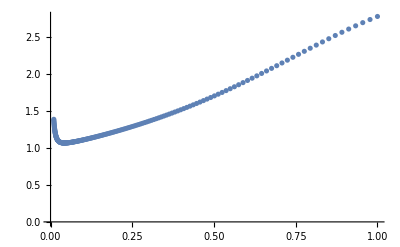

```mathematica
ListPlot[%]
```